```mathematica
ClearAll["Global`*"]
```

Path to the density profiles (“ density maps”)

```mathematica
PathMD="/Volumes/UNI/planar_densmaps_Version_v2/";
```

Positions of the last peak in the density of each SAM

```mathematica
peak0=10.950001
peak11=10.950001
peak22=9.860000
peak33=10.950001
peak37=10.950001
peak44=9.860000
peak50=9.860000
```

10.95

10.95

9.86

10.95

10.95

9.86

9.86

```mathematica
(*Horizontal line at the theoretical value of 1000kg/m3 of the water bulk density*)
bulkLine=Line[{{-3,1000},{3,1000}}];
```

## SAM 0 %

## FIRST : we plot all density profiles to determine the interval where the water density has a stable bulk value. In order to do so we store the density values as lists in separate variables. For example (for the surface with 0% -OH coverage): WaterData0 and SurfData0 for mass densities (number densities not used anymore!!) We store the beginning and ending of each bulk interval as start0 and end0 or start22 and end22 for example.

### Mass Density

Store water mass density of SAM 0 % in Waterdata0

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_NVT_sam0_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
WaterData0 = Take[input,{start+1,Length[input]}];
```

Shift the z - coordinates to obtain the same coordinates as in original ".gro" file

```mathematica
(*The coordinates of the first and last slices will be useful later, specially for the plots*)
firstSliceCoord=WaterData0[[All,1]][[1]]
WaterData0=WaterData0[[All,1]]-firstSliceCoord;
firstSliceCoord=WaterData0[[All,1]][[1]]
lastSliceCoord=WaterData0[[All,1]][[-1]]
```

Part::partd: Part specification {0., 0.00304, 0.00608, 0.00912, 0.01216, 0.01521, 0.01825, 0.02129, 0.02433, 0.02737, « 31 », 0.12468, 0.12772, 0.13076, 0.1338, 0.13685, 0.13989, 0.14293, 0.14597, 0.14901, « 950 »} is longer than depth of object.

{0.,0.00304,0.00608,0.00912,0.01216,0.01521,0.01825,0.02129,0.02433,0.02737,0.03041,0.03345,0.03649,0.03953,0.04257,0.04562,0.04866,0.0517,0.05474,0.05778,0.06082,0.06386,0.0669,0.06994,0.07298,0.07603,0.07907,0.08211,0.08515,0.08819,0.09123,0.09427,0.09731,0.10035,0.10339,0.10644,0.10948,0.11252,0.11556,0.1186,0.12164,0.12468,0.12772,0.13076,0.1338,0.13685,0.13989,0.14293,0.14597,0.14901,0.15205,0.15509,0.15813,0.16117,0.16421,0.16726,0.1703,0.17334,0.17638,0.17942,0.18246,0.1855,0.18854,0.19158,0.19462,0.19767,0.20071,0.20375,0.20679,0.20983,0.21287,0.21591,0.21895,0.22199,0.22503,0.22808,0.23112,0.23416,0.2372,0.24024,0.24328,0.24632,0.24936,0.2524,0.25544,0.25849,0.26153,0.26457,0.26761,0.27065,0.27369,0.27673,0.27977,0.28281,0.28585,0.2889,0.29194,0.29498,0.29802,0.30106,0.3041,0.30714,0.31018,0.31322,0.31626,0.31931,0.32235,0.32539,0.32843,0.33147,0.33451,0.33755,0.34059,0.34363,0.34667,0.34972,0.35276,0.3558,0.35884,0.36188,0.36492,0.36796,0.371,0.37404,0.37708,0.38013,0.38317,0.38621,0.38925,0.39229,0.39533,0.39837,0.40141,0.40445,0.40749,0.41054,0.41358,0.41662,0.41966,0.4227,0.42574,0.42878,0.43182,0.43486,0.4379,0.44095,0.44399,0.44703,0.45007,0.45311,0.45615,0.45919,0.46223,0.46527,0.46831,0.47136,0.4744,0.47744,0.48048,0.48352,0.48656,0.4896,0.49264,0.49568,0.49872,0.50177,0.50481,0.50785,0.51089,0.51393,0.51697,0.520012,0.523053,0.526094,0.529135,0.532176,0.535217,0.538258,0.541299,0.54434,0.547381,0.550422,0.553463,0.556504,0.559545,0.562586,0.565627,0.568668,0.571709,0.57475,0.577791,0.580832,0.583873,0.586914,0.589955,0.592996,0.596037,0.599078,0.602119,0.60516,0.608201,0.611242,0.614283,0.617324,0.620365,0.623406,0.626447,0.629488,0.632529,0.63557,0.638611,0.641652,0.644693,0.647734,0.650775,0.653816,0.656857,0.659898,0.662939,0.66598,0.669021,0.672062,0.675103,0.678144,0.681185,0.684226,0.687267,0.690308,0.693349,0.69639,0.699431,0.702472,0.705513,0.708554,0.711595,0.714636,0.717677,0.720718,0.723759,0.7268,0.729841,0.732882,0.735923,0.738964,0.742005,0.745046,0.748087,0.751128,0.754169,0.75721,0.760251,0.763292,0.766333,0.769374,0.772415,0.775456,0.778497,0.781538,0.784579,0.78762,0.790661,0.793702,0.796743,0.799784,0.802825,0.805866,0.808907,0.811948,0.814989,0.81803,0.821071,0.824112,0.827153,0.830194,0.833235,0.836276,0.839317,0.842358,0.845399,0.84844,0.851481,0.854522,0.857563,0.860604,0.863645,0.866686,0.869727,0.872768,0.875809,0.87885,0.881891,0.884932,0.887973,0.891014,0.894055,0.897096,0.900137,0.903178,0.906219,0.90926,0.912301,0.915342,0.918382,0.921424,0.924464,0.927506,0.930546,0.933588,0.936629,0.93967,0.942711,0.945752,0.948793,0.951834,0.954875,0.957916,0.960957,0.963998,0.967039,0.97008,0.973121,0.976162,0.979203,0.982244,0.985285,0.988326,0.991367,0.994408,0.997449,1.00049,1.00353,1.00657,1.00961,1.01265,1.0157,1.01874,1.02178,1.02482,1.02786,1.0309,1.03394,1.03698,1.04002,1.04306,1.04611,1.04915,1.05219,1.05523,1.05827,1.06131,1.06435,1.06739,1.07043,1.07347,1.07652,1.07956,1.0826,1.08564,1.08868,1.09172,1.09476,1.0978,1.10084,1.10388,1.10693,1.10997,1.11301,1.11605,1.11909,1.12213,1.12517,1.12821,1.13125,1.13429,1.13734,1.14038,1.14342,1.14646,1.1495,1.15254,1.15558,1.15862,1.16166,1.1647,1.16775,1.17079,1.17383,1.17687,1.17991,1.18295,1.18599,1.18903,1.19207,1.19511,1.19815,1.2012,1.20424,1.20728,1.21032,1.21336,1.2164,1.21944,1.22248,1.22552,1.22857,1.23161,1.23465,1.23769,1.24073,1.24377,1.24681,1.24985,1.25289,1.25593,1.25897,1.26202,1.26506,1.2681,1.27114,1.27418,1.27722,1.28026,1.2833,1.28634,1.28939,1.29243,1.29547,1.29851,1.30155,1.30459,1.30763,1.31067,1.31371,1.31675,1.3198,1.32284,1.32588,1.32892,1.33196,1.335,1.33804,1.34108,1.34412,1.34716,1.3502,1.35325,1.35629,1.35933,1.36237,1.36541,1.36845,1.37149,1.37453,1.37757,1.38062,1.38366,1.3867,1.38974,1.39278,1.39582,1.39886,1.4019,1.40494,1.40798,1.41103,1.41407,1.41711,1.42015,1.42319,1.42623,1.42927,1.43231,1.43535,1.43839,1.44143,1.44448,1.44752,1.45056,1.4536,1.45664,1.45968,1.46272,1.46576,1.4688,1.47184,1.47489,1.47793,1.48097,1.48401,1.48705,1.49009,1.49313,1.49617,1.49921,1.50225,1.5053,1.50834,1.51138,1.51442,1.51746,1.5205,1.52354,1.52658,1.52962,1.53266,1.53571,1.53875,1.54179,1.54483,1.54787,1.55091,1.55395,1.55699,1.56003,1.56307,1.56612,1.56916,1.5722,1.57524,1.57828,1.58132,1.58436,1.5874,1.59044,1.59348,1.59653,1.59957,1.60261,1.60565,1.60869,1.61173,1.61477,1.61781,1.62085,1.62389,1.62694,1.62998,1.63302,1.63606,1.6391,1.64214,1.64518,1.64822,1.65126,1.6543,1.65735,1.66039,1.66343,1.66647,1.66951,1.67255,1.67559,1.67863,1.68167,1.68471,1.68776,1.6908,1.69384,1.69688,1.69992,1.70296,1.706,1.70904,1.71208,1.71512,1.71817,1.72121,1.72425,1.72729,1.73033,1.73337,1.73641,1.73945,1.74249,1.74553,1.74858,1.75162,1.75466,1.7577,1.76074,1.76378,1.76682,1.76986,1.7729,1.77594,1.77899,1.78203,1.78507,1.78811,1.79115,1.79419,1.79723,1.80027,1.80331,1.80635,1.80939,1.81244,1.81548,1.81852,1.82156,1.8246,1.82764,1.83068,1.83372,1.83676,1.83981,1.84285,1.84589,1.84893,1.85197,1.85501,1.85805,1.86109,1.86413,1.86717,1.87022,1.87326,1.8763,1.87934,1.88238,1.88542,1.88846,1.8915,1.89454,1.89758,1.90063,1.90367,1.90671,1.90975,1.91279,1.91583,1.91887,1.92191,1.92495,1.92799,1.93104,1.93408,1.93712,1.94016,1.9432,1.94624,1.94928,1.95232,1.95536,1.9584,1.96144,1.96449,1.96753,1.97057,1.97361,1.97665,1.97969,1.98273,1.98577,1.98881,1.99186,1.9949,1.99794,2.00098,2.00402,2.00706,2.0101,2.01314,2.01618,2.01922,2.02227,2.02531,2.02835,2.03139,2.03443,2.03747,2.04051,2.04355,2.04659,2.04963,2.05268,2.05572,2.05876,2.0618,2.06484,2.06788,2.07092,2.07396,2.077,2.08004,2.08309,2.08613,2.08917,2.09221,2.09525,2.09829,2.10133,2.10437,2.10741,2.11045,2.1135,2.11654,2.11958,2.12262,2.12566,2.1287,2.13174,2.13478,2.13782,2.14086,2.14391,2.14695,2.14999,2.15303,2.15607,2.15911,2.16215,2.16519,2.16823,2.17127,2.17432,2.17736,2.1804,2.18344,2.18648,2.18952,2.19256,2.1956,2.19864,2.20168,2.20473,2.20777,2.21081,2.21385,2.21689,2.21993,2.22297,2.22601,2.22905,2.23209,2.23514,2.23818,2.24122,2.24426,2.2473,2.25034,2.25338,2.25642,2.25946,2.2625,2.26555,2.26859,2.27163,2.27467,2.27771,2.28075,2.28379,2.28683,2.28987,2.29291,2.29596,2.299,2.30204,2.30508,2.30812,2.31116,2.3142,2.31724,2.32028,2.32332,2.32637,2.32941,2.33245,2.33549,2.33853,2.34157,2.34461,2.34765,2.35069,2.35373,2.35678,2.35982,2.36286,2.3659,2.36894,2.37198,2.37502,2.37806,2.3811,2.38414,2.38719,2.39023,2.39327,2.39631,2.39935,2.40239,2.40543,2.40847,2.41151,2.41455,2.4176,2.42064,2.42368,2.42672,2.42976,2.4328,2.43584,2.43888,2.44192,2.44496,2.44801,2.45105,2.45409,2.45713,2.46017,2.46321,2.46625,2.46929,2.47233,2.47537,2.47842,2.48146,2.4845,2.48754,2.49058,2.49362,2.49666,2.4997,2.50274,2.50578,2.50883,2.51187,2.51491,2.51795,2.52099,2.52403,2.52707,2.53011,2.53315,2.53619,2.53924,2.54228,2.54532,2.54836,2.5514,2.55444,2.55748,2.56052,2.56356,2.5666,2.56965,2.57269,2.57573,2.57877,2.58181,2.58485,2.58789,2.59093,2.59397,2.59701,2.60006,2.6031,2.60614,2.60918,2.61222,2.61526,2.6183,2.62134,2.62438,2.62742,2.63047,2.63351,2.63655,2.63959,2.64263,2.64567,2.64871,2.65175,2.65479,2.65783,2.66088,2.66392,2.66696,2.67,2.67304,2.67608,2.67912,2.68216,2.6852,2.68824,2.69129,2.69433,2.69737,2.70041,2.70345,2.70649,2.70953,2.71257,2.71561,2.71865,2.7217,2.72474,2.72778,2.73082,2.73386,2.7369,2.73994,2.74298,2.74602,2.74906,2.75211,2.75515,2.75819,2.76123,2.76427,2.76731,2.77035,2.77339,2.77643,2.77947,2.78252,2.78556,2.7886,2.79164,2.79468,2.79772,2.80076,2.8038,2.80684,2.80988,2.81293,2.81597,2.81901,2.82205,2.82509,2.82813,2.83117,2.83421,2.83725,2.84029,2.84334,2.84638,2.84942,2.85246,2.8555,2.85854,2.86158,2.86462,2.86766,2.8707,2.87375,2.87679,2.87983,2.88287,2.88591,2.88895,2.89199,2.89503,2.89807,2.90111,2.90416,2.9072,2.91024,2.91328,2.91632,2.91936,2.9224,2.92544,2.92848,2.93152,2.93457,2.93761,2.94065,2.94369,2.94673,2.94977,2.95281,2.95585,2.95889,2.96193,2.96498,2.96802,2.97106,2.9741,2.97714,2.98018,2.98322,2.98626,2.9893,2.99234,2.99539,2.99843,3.00147,3.00451,3.00755,3.01059,3.01363,3.01667,3.01971,3.02275,3.0258,3.02884,3.03188,3.03492,3.03796}

Part::partd: Part specification {0., 0.00304, 0.00608, 0.00912, 0.01216, 0.01521, 0.01825, 0.02129, 0.02433, 0.02737, « 31 », 0.12468, 0.12772, 0.13076, 0.1338, 0.13685, 0.13989, 0.14293, 0.14597, 0.14901, « 950 »} is longer than depth of object.

Part::partd: Part specification {0., 0.00304, 0.00608, 0.00912, 0.01216, 0.01521, 0.01825, 0.02129, 0.02433, 0.02737, « 32 », 0.12772, 0.13076, 0.1338, 0.13685, 0.13989, 0.14293, 0.14597, 0.14901, « 950 »} ⟦ All, 1 ⟧ is longer than depth of object.

0.

-3.03796

Store the surface mass density of SAM 0 % in SurfData0

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_SAM_sam0_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
SurfData0 = Take[input,{start+1,Length[input]}];
```

Shift the z - coordinates to obtain the same coordinates as in original ".gro" file

```mathematica
SurfData0=SurfData0-firstSliceCoord;
```

Plot water and surface (mass) densities together

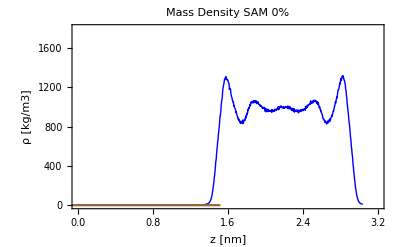

```mathematica
waterplot0=ListPlot[WaterData0,Joined->True,PlotStyle->{Blue,Thick}];
surfplot0=ListPlot[SurfData0,Joined->True,PlotStyle->{Brown}];
plot0=Show[waterplot0,surfplot0,PlotLabel->"Mass Density SAM 0%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{0,3.2},{0,1800}}]
```

Zoom on bulk interval and add horizontal line at bulk value (1000 kg/m3) (“bulkLine” defined at beginning of notebook)

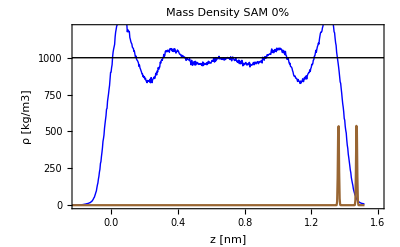

```mathematica
plot0zoom=Show[waterplot0,surfplot0,PlotLabel->"Mass Density SAM 0%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}}, Epilog-> bulkLine]
```

Define beginning and ending positions of bulk density interval AND show as vertical lines on last density plot: 
- determine position of first intersection after first water peak (right-click to “get coordinates” manually) => store in start0
- determine position of last intersection before last water peak => store in end0
- make same plot again with vertical lines to “finetune” the values (and as a check)

```mathematica
start0=0.308;
end0=1.059;
start0Line=Line[{{start0,0},{start0,1500}}];
end0Line=Line[{{end0,0},{end0,1500}}];
```

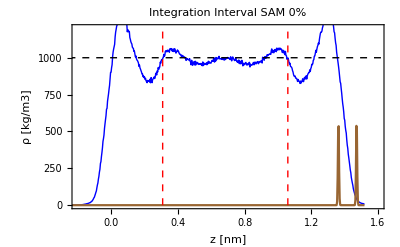

```mathematica
plot0zoom=Show[waterplot0,surfplot0,PlotLabel->"Integration Interval SAM 0%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}},Epilog->{Dashed,bulkLine,Red,start0Line,end0Line}]
```

ONLY ONCE!! =>  Determine length of each interval in z - direction and the coordinates of the first and last slices (ONLY ONCE! since all systems are divided in the same manner. Values can be used for all systems)

```mathematica
(* Coordinate of last slice*) 
WaterData0[[All,1]][[-1]];
(* Coordinate of slice before the last*) 
WaterData0[[All,1]][[-2]];
(* z-length of slice is the difference between neighbour slices*) 
sliceLength=Abs[WaterData0[[All,1]][[-1]]-WaterData0[[All,1]][[-2]]];
```

Determine average water bulk density by calculating the mean value of the density inside the previously determined “bulk interval” between start0 and end0:
- both coordinates have to be “translated” into the interval (slice) number. For example, the position -1.0nm could be inside the 33th slice or interval.

```mathematica
(*Slice number of start0*)
start0SliceNum=Round[Abs[start0-firstSliceCoord]/sliceLength]+1;
(*Slice number of end0*)
end0SliceNum=Round[Abs[end0-firstSliceCoord]/sliceLength]+1;
(*bulk density*)
bulk0 = Mean[WaterData0[[All,2]][[start0SliceNum;;end0SliceNum]]]
Print["water: mean value of num density = ",bulk0]
```

996.54

water: mean value of num density = 996.54

Determine GDS position acording to Gibbs definition (integral equation). We assume that the whole system ends at “end0” where the density value is still the bulk (thus the integral goes from the beginning of the system to “end0” and we ignore the rest)

```mathematica
GDS0=end0-Integrate[Interpolation[WaterData0][x],{x,firstSliceCoord,end0}]/bulk0
```

-0.0553131

Plot again the density showing the GDS position and the bulk value as lines.

Line[{{-0.0553131,0},{-0.0553131,1500}}]

Line[{{-1.51898,996.54},{1.51898,996.54}}]

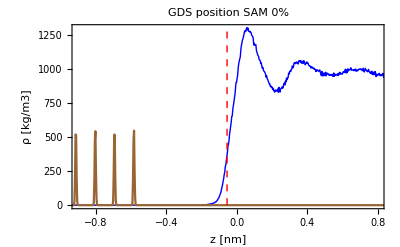

```mathematica
lineGDS0=Line[{{GDS0,0},{GDS0,1500}}]
lineBulk0=Line[{{firstSliceCoord,bulk0},{lastSliceCoord,bulk0}}]
plotGDS0=Show[waterplot0,surfplot0,PlotLabel->"GDS position SAM 0%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.9,0.8},{0,1300}},Epilog->{Red,Thick,Dashed,lineGDS0}]
```

Calculate difference between GDS position and last peak in the SAM density (to extrapolate the GDS position of the droplet systems using the SAM as a reference).

## SAM 11 %

### Mass Density

Store water mass density of SAM 11 % in Waterdata11

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_NVT_sam11_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
WaterData11 = Take[input,{start+1,Length[input]}];
```

Store the surface mass density of SAM 11 % in SurfData11

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"ndens_SAM_sam11_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
SurfData11 = Take[input,{start+1,Length[input]}];
```

Plot water and surface (mass) densities together

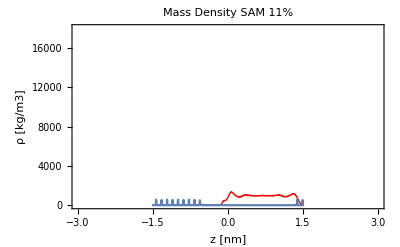

```mathematica
waterplot11=ListPlot[WaterData11,Joined->True,PlotStyle->{Red,Thick}];
surfplot11=ListPlot[SurfData11,Joined->True];
plot11=Show[waterplot11,surfplot11,PlotLabel->"Mass Density SAM 11%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-3,3.},{0,18000}}]
```

Zoom on bulk interval and add horizontal line at bulk value (1000 kg/m3) (“bulkLine” defined at beginning of notebook)

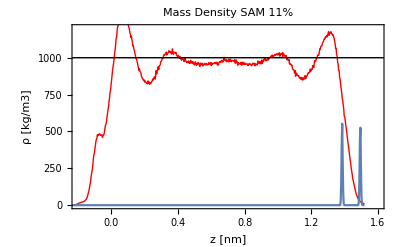

```mathematica
waterplot11=ListPlot[WaterData11,Joined->True,PlotStyle->{Red,Thick}];
surfplot11=ListPlot[SurfData11,Joined->True];
plot11zoom=Show[waterplot11,surfplot11,PlotLabel->"Mass Density SAM 11%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}}, Epilog-> bulkLine]
```

Define beginning and ending positions of integration interval AND show as vertical lines on last density plot: 
- determine position of first intersection after first water peak (right-click to “get coordinates” manually) => store in start0
- determine position of last intersection before last water peak => store in end0
- make same plot again with vertical lines to “finetune” the values (and as a check)

```mathematica
start11=0.302;
end11=1.059;
start11Line=Line[{{start11,0},{start11,1500}}];
end11Line=Line[{{end11,0},{end11,1500}}];
```

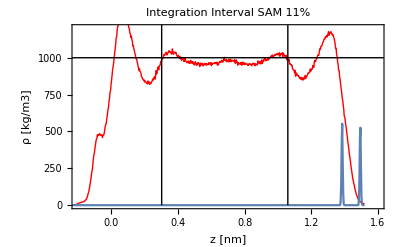

```mathematica
waterplot11=ListPlot[WaterData11,Joined->True,PlotStyle->{Red,Thick}];
surfplot11=ListPlot[SurfData11,Joined->True];
plot11zoom=Show[waterplot11,surfplot11,PlotLabel->"Integration Interval SAM 11%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}},Epilog->{bulkLine,start11Line,end11Line}]
```

## SAM 22 %

### Mass Density

Store water mass density of SAM 22 % in Waterdata22

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_NVT_sam22_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
WaterData22 = Take[input,{start+1,Length[input]}];
```

Store the surface mass density of SAM 22 % in SurfData22

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_SAM_sam22_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
SurfData22 = Take[input,{start+1,Length[input]}];
```

Plot water and surface (mass) densities together

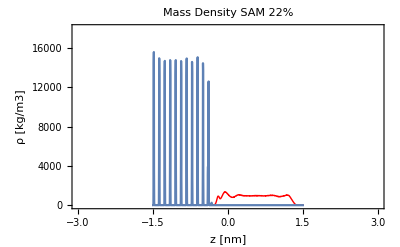

```mathematica
waterplot22=ListPlot[WaterData22,Joined->True,PlotStyle->{Red,Thick}];
surfplot22=ListPlot[SurfData22,Joined->True];
plot22=Show[waterplot22,surfplot22,PlotLabel->"Mass Density SAM 22%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-3,3.},{0,18000}}]
```

Zoom on bulk interval and add horizontal line at bulk value (1000 kg/m3) (“bulkLine” defined at beginning of notebook)

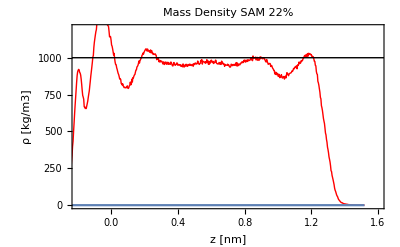

```mathematica
waterplot22=ListPlot[WaterData22,Joined->True,PlotStyle->{Red,Thick}];
surfplot22=ListPlot[SurfData22,Joined->True];
plot22zoom=Show[waterplot22,surfplot22,PlotLabel->"Mass Density SAM 22%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}}, Epilog-> bulkLine]
```

Define beginning and ending positions of integration interval AND show as vertical lines on last density plot: 
- determine position of first intersection after first water peak (right-click to “get coordinates” manually) => store in start0
- determine position of last intersection before last water peak => store in end0
- make same plot again with vertical lines to “finetune” the values (and as a check)

```mathematica
start22=0.302;
end22=1.059;
start22Line=Line[{{start22,0},{start22,1500}}];
end22Line=Line[{{end22,0},{end22,1500}}];
```

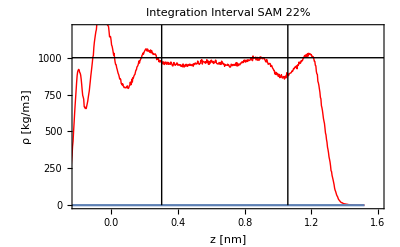

```mathematica
waterplot22=ListPlot[WaterData22,Joined->True,PlotStyle->{Red,Thick}];
surfplot22=ListPlot[SurfData22,Joined->True];
plot22zoom=Show[waterplot22,surfplot22,PlotLabel->"Integration Interval SAM 22%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}},Epilog->{bulkLine,start22Line,end22Line}]
```

## SAM 33 %

### Mass Density

Store water mass density of SAM 33 % in Waterdata33

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_NVT_sam33_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
WaterData33 = Take[input,{start+1,Length[input]}];
```

Store the surface mass density of SAM 33 % in SurfData33

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_SAM_sam33_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
SurfData33 = Take[input,{start+1,Length[input]}];
```

Plot water and surface (mass) densities together

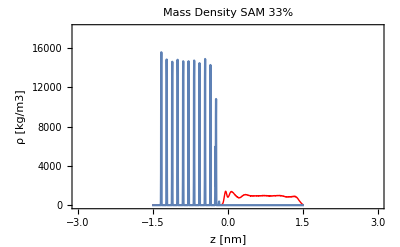

```mathematica
waterplot33=ListPlot[WaterData33,Joined->True,PlotStyle->{Red,Thick}];
surfplot33=ListPlot[SurfData33,Joined->True];
plot33=Show[waterplot33,surfplot33,PlotLabel->"Mass Density SAM 33%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-3,3.},{0,18000}}]
```

Zoom on bulk interval and add horizontal line at bulk value (1000 kg/m3) (“bulkLine” defined at beginning of notebook)

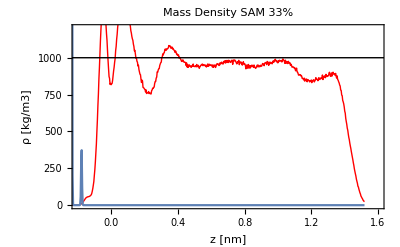

```mathematica
waterplot33=ListPlot[WaterData33,Joined->True,PlotStyle->{Red,Thick}];
surfplot33=ListPlot[SurfData33,Joined->True];
plot33zoom=Show[waterplot33,surfplot33,PlotLabel->"Mass Density SAM 33%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}}, Epilog-> bulkLine]
```

Define beginning and ending positions of integration interval AND show as vertical lines on last density plot: 
- determine position of first intersection after first water peak (right-click to “get coordinates” manually) => store in start0
- determine position of last intersection before last water peak => store in end0
- make same plot again with vertical lines to “finetune” the values (and as a check)

```mathematica
start33=0.302;
end33=1.059;
start33Line=Line[{{start33,0},{start33,1500}}];
end33Line=Line[{{end33,0},{end33,1500}}];
```

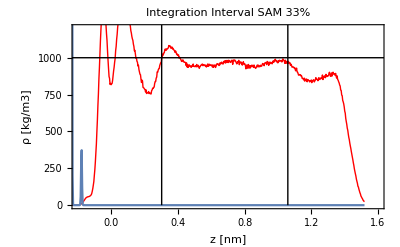

```mathematica
waterplot33=ListPlot[WaterData33,Joined->True,PlotStyle->{Red,Thick}];
surfplot33=ListPlot[SurfData33,Joined->True];
plot33zoom=Show[waterplot33,surfplot33,PlotLabel->"Integration Interval SAM 33%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}},Epilog->{bulkLine,start33Line,end33Line}]
```

## SAM 37 %

### Mass Density

Store water mass density of SAM 37 % in Waterdata37

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_NVT_sam37_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
WaterData37 = Take[input,{start+1,Length[input]}];
```

Store the surface mass density of SAM 37 % in SurfData37

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_SAM_sam37_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
SurfData37 = Take[input,{start+1,Length[input]}];
```

Plot water and surface (mass) densities together

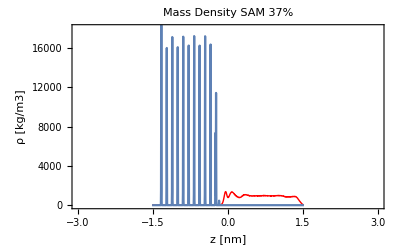

```mathematica
waterplot37=ListPlot[WaterData37,Joined->True,PlotStyle->{Red,Thick}];
surfplot37=ListPlot[SurfData37,Joined->True];
plot37=Show[waterplot37,surfplot37,PlotLabel->"Mass Density SAM 37%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-3,3.},{0,18000}}]
```

Zoom on bulk interval and add horizontal line at bulk value (1000 kg/m3) (“bulkLine” defined at beginning of notebook)

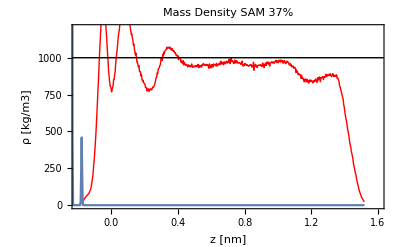

```mathematica
waterplot37=ListPlot[WaterData37,Joined->True,PlotStyle->{Red,Thick}];
surfplot37=ListPlot[SurfData37,Joined->True];
plot37zoom=Show[waterplot37,surfplot37,PlotLabel->"Mass Density SAM 37%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}}, Epilog-> bulkLine]
```

Define beginning and ending positions of integration interval AND show as vertical lines on last density plot: 
- determine position of first intersection after first water peak (right-click to “get coordinates” manually) => store in start0
- determine position of last intersection before last water peak => store in end0
- make same plot again with vertical lines to “finetune” the values (and as a check)

```mathematica
start37=0.302;
end37=1.059;
start37Line=Line[{{start37,0},{start37,1500}}];
end37Line=Line[{{end37,0},{end37,1500}}];
```

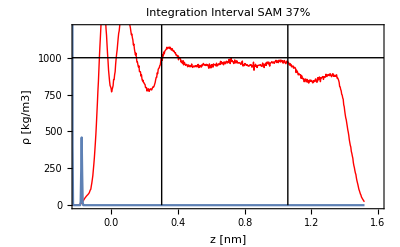

```mathematica
waterplot37=ListPlot[WaterData37,Joined->True,PlotStyle->{Red,Thick}];
surfplot37=ListPlot[SurfData37,Joined->True];
plot37zoom=Show[waterplot37,surfplot37,PlotLabel->"Integration Interval SAM 37%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}},Epilog->{bulkLine,start37Line,end37Line}]
```

## SAM 44 %

### Mass Density

Store water mass density of SAM 44 % in Waterdata44

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_NVT_sam44_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
WaterData44 = Take[input,{start+1,Length[input]}];
```

Store the surface mass density of SAM 44 % in SurfData44

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_SAM_sam44_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
SurfData44 = Take[input,{start+1,Length[input]}];
```

Plot water and surface (mass) densities together

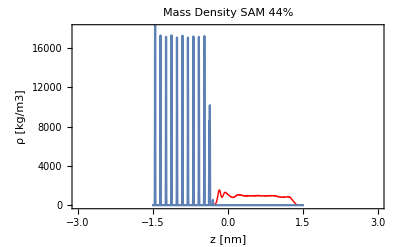

```mathematica
waterplot44=ListPlot[WaterData44,Joined->True,PlotStyle->{Red,Thick}];
surfplot44=ListPlot[SurfData44,Joined->True];
plot44=Show[waterplot44,surfplot44,PlotLabel->"Mass Density SAM 44%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-3,3.},{0,18000}}]
```

Zoom on bulk interval and add horizontal line at bulk value (1000 kg/m3) (“bulkLine” defined at beginning of notebook)

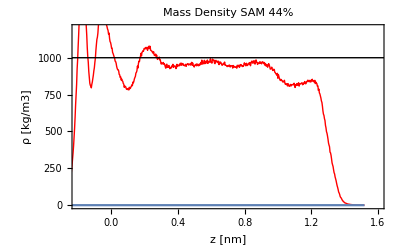

```mathematica
waterplot44=ListPlot[WaterData44,Joined->True,PlotStyle->{Red,Thick}];
surfplot44=ListPlot[SurfData44,Joined->True];
plot44zoom=Show[waterplot44,surfplot44,PlotLabel->"Mass Density SAM 44%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}}, Epilog-> bulkLine]
```

Define beginning and ending positions of integration interval AND show as vertical lines on last density plot: 
- determine position of first intersection after first water peak (right-click to “get coordinates” manually) => store in start0
- determine position of last intersection before last water peak => store in end0
- make same plot again with vertical lines to “finetune” the values (and as a check)

```mathematica
start44=0.302;
end44=1.059;
start44Line=Line[{{start44,0},{start44,1500}}];
end44Line=Line[{{end44,0},{end44,1500}}];
```

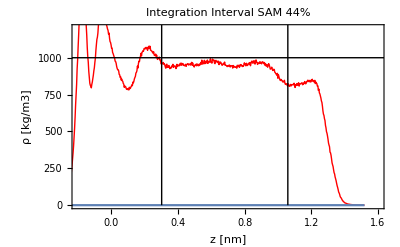

```mathematica
waterplot44=ListPlot[WaterData44,Joined->True,PlotStyle->{Red,Thick}];
surfplot44=ListPlot[SurfData44,Joined->True];
plot44zoom=Show[waterplot44,surfplot44,PlotLabel->"Integration Interval SAM 44%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}},Epilog->{bulkLine,start44Line,end44Line}]
```